## Problem 2

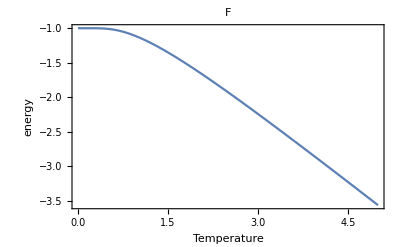

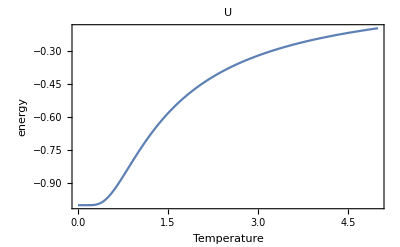

General::munfl: Sech[9790.21] is too small to represent as a normalized machine number; precision may be lost.

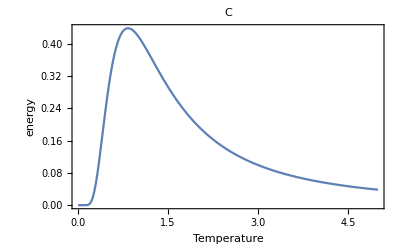

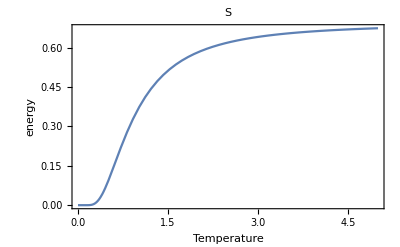

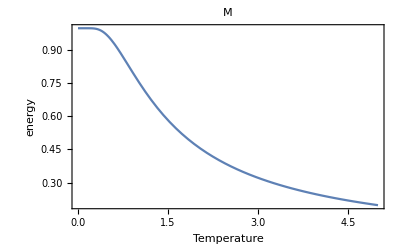

```mathematica
Plot[-T*Log[2*Cosh[1/T]],{T,0,5},{Frame->True,PlotRange->All,BaseStyle->{FontSize->12},PlotLabel->F, FrameLabel->{"Temperature","energy"}}]
Plot[-Tanh[1/T],{T,0,5},{Frame->True,PlotRange->All,BaseStyle->{FontSize->12},PlotLabel->U,FrameLabel->{"Temperature","energy"}}]
Plot[(1/T^2)*(Sech[1/T])^2,{T,0,5},{Frame->True,PlotRange->All,BaseStyle->{FontSize->12},PlotLabel->C,FrameLabel->{"Temperature","energy"}}]
Plot[(-1/T*Tanh[1/T])+(Log[2*Cosh[1/T]]),{T,0,5},{Frame->True,PlotRange->All,BaseStyle->{FontSize->12},PlotLabel->S,FrameLabel->{"Temperature","energy"}}]
Plot[Tanh[1/T],{T,0,5},{Frame->True,PlotRange->All,BaseStyle->{FontSize->12},PlotLabel->M,FrameLabel->{"Temperature","energy"}}]
```